```mathematica
Clear["Global`*"]
```

```mathematica
Subscript[x, 1][t]
```

InterpolatingFunction[…]

```mathematica
por=Table[Subscript[r, i][t],{i,1,3}];po=Table[por[[i]]={Subscript[x, i][t],Subscript[y, i][t],Subscript[z, i][t]},{i,1,3}];vpo=Flatten[Table[por[[i]]={Subscript[x, i][t],Subscript[y, i][t],Subscript[z, i][t]},{i,1,3}]];fpo=Flatten[D[po,t,t]];vi=Flatten[D[po,t]];mass={2,1,1};
(*Table[Subscript[mas, i],{i,1,3}]*);
```

```mathematica
ac=Flatten[Table[Sum[If[m≠n,mass[[m]](po[[n]]-po[[m]])/Norm[(po[[n]]-po[[m]])]^3,0],{m,1,3}],{n,1,3}]];
```

```mathematica
eqs=Flatten[Table[fpo[[n]]==ac[[n]],{n,1,9}]];po2=Flatten[Table[por[[i]]={Subscript[x, i],Subscript[y, i],Subscript[z, i]},{i,1,3}]];vel2=Flatten[Table[por[[i]]={Subscript[x, i]',Subscript[y, i]',Subscript[z, i]'},{i,1,3}]];myfunc[f_,x_]:=po2[[#1]]/@{#2}&[f,x];intpos=Flatten[Table[myfunc[i,0],{i,1,9}]];
vfunc[f_,x_]:=vel2[[#1]]/@{#2}&[f,x];intvel=Flatten[Table[vfunc[i,0],{i,1,9}]];
invel=Table[intvel[[i]]==RandomReal[1,9][[i]],{i,9}]
inr=Table[intpos[[i]]==RandomReal[1,9][[i]],{i,9}]
```

```mathematica
Subscript[x, 1][t]
```

InterpolatingFunction[…]

```mathematica
sol=NDSolve[{eqs,{Subscript[x, 1][0]==0.6177516682593021,Subscript[y, 1][0]==0.4832988153354689,Subscript[z, 1][0]==0.24145487005568977,Subscript[x, 2][0]==0.553306942631284,Subscript[y, 2][0]==0.2261938984671159,Subscript[z, 2][0]==0.5998483934922467,Subscript[x, 3][0]==0.7196188901663974,Subscript[y, 3][0]==0.875702950090083,Subscript[z, 3][0]==0.4576303089481064},{Subscript[x, 1]'[0]==0,Subscript[y, 1]'[0]==0.3533517225905536,Subscript[z, 1]'[0]==0.37831366628698126,Subscript[x, 2]'[0]==0.9627379074564417,Subscript[y, 2]'[0]==0.4164229692820276,Subscript[z, 2]'[0]==0.6340655845962282,Subscript[x, 3]'[0]==0.13798661803128476,Subscript[y, 3]'[0]==0.7043227072938394,Subscript[z, 3]'[0]==0.3707019436501042}},vpo,{t,0,10}]
```

NDSolve::ndode: The equations {x_1'[0]==0} are not differential equations or initial conditions in the dependent variables {TemporaryVariable$296056,TemporaryVariable$296057,TemporaryVariable$296058,TemporaryVariable$296059,TemporaryVariable$296060,TemporaryVariable$296061,TemporaryVariable$296062,TemporaryVariable$296063}.

NDSolve[{{0==(InterpolatingFunction[…]-x_2[t])/((Abs[InterpolatingFunction[…]-x_2[t]]^2+Abs[y_1[t]-y_2[t]]^2+Abs[z_1[t]-z_2[t]]^2)^(3/2))+(InterpolatingFunction[…]-x_3[t])/((Abs[InterpolatingFunction[…]-x_3[t]]^2+Abs[y_1[t]-y_3[t]]^2+Abs[z_1[t]-z_3[t]]^2)^(3/2)),y_1''[t]==(y_1[t]-y_2[t])/((Abs[InterpolatingFunction[…]-x_2[t]]^2+Abs[y_1[t]-y_2[t]]^2+Abs[z_1[t]-z_2[t]]^2)^(3/2))+(y_1[t]-y_3[t])/((Abs[InterpolatingFunction[…]-x_3[t]]^2+Abs[y_1[t]-y_3[t]]^2+Abs[z_1[t]-z_3[t]]^2)^(3/2)),z_1''[t]==(z_1[t]-z_2[t])/((Abs[InterpolatingFunction[…]-x_2[t]]^2+Abs[y_1[t]-y_2[t]]^2+Abs[z_1[t]-z_2[t]]^2)^(3/2))+(z_1[t]-z_3[t])/((Abs[InterpolatingFunction[…]-x_3[t]]^2+Abs[y_1[t]-y_3[t]]^2+Abs[z_1[t]-z_3[t]]^2)^(3/2)),x_2''[t]==(1.5 (-InterpolatingFunction[…]+x_2[t]))/((Abs[-InterpolatingFunction[…]+x_2[t]]^2+Abs[-y_1[t]+y_2[t]]^2+Abs[-z_1[t]+z_2[t]]^2)^(3/2))+(x_2[t]-x_3[t])/((Abs[x_2[t]-x_3[t]]^2+Abs[y_2[t]-y_3[t]]^2+Abs[z_2[t]-z_3[t]]^2)^(3/2)),y_2''[t]==(1.5 (-y_1[t]+y_2[t]))/((Abs[-InterpolatingFunction[…]+x_2[t]]^2+Abs[-y_1[t]+y_2[t]]^2+Abs[-z_1[t]+z_2[t]]^2)^(3/2))+(y_2[t]-y_3[t])/((Abs[x_2[t]-x_3[t]]^2+Abs[y_2[t]-y_3[t]]^2+Abs[z_2[t]-z_3[t]]^2)^(3/2)),z_2''[t]==(1.5 (-z_1[t]+z_2[t]))/((Abs[-InterpolatingFunction[…]+x_2[t]]^2+Abs[-y_1[t]+y_2[t]]^2+Abs[-z_1[t]+z_2[t]]^2)^(3/2))+(z_2[t]-z_3[t])/((Abs[x_2[t]-x_3[t]]^2+Abs[y_2[t]-y_3[t]]^2+Abs[z_2[t]-z_3[t]]^2)^(3/2)),x_3''[t]==(1.5 (-InterpolatingFunction[…]+x_3[t]))/((Abs[-InterpolatingFunction[…]+x_3[t]]^2+Abs[-y_1[t]+y_3[t]]^2+Abs[-z_1[t]+z_3[t]]^2)^(3/2))+(-x_2[t]+x_3[t])/((Abs[-x_2[t]+x_3[t]]^2+Abs[-y_2[t]+y_3[t]]^2+Abs[-z_2[t]+z_3[t]]^2)^(3/2)),y_3''[t]==(1.5 (-y_1[t]+y_3[t]))/((Abs[-InterpolatingFunction[…]+x_3[t]]^2+Abs[-y_1[t]+y_3[t]]^2+Abs[-z_1[t]+z_3[t]]^2)^(3/2))+(-y_2[t]+y_3[t])/((Abs[-x_2[t]+x_3[t]]^2+Abs[-y_2[t]+y_3[t]]^2+Abs[-z_2[t]+z_3[t]]^2)^(3/2)),z_3''[t]==(1.5 (-z_1[t]+z_3[t]))/((Abs[-InterpolatingFunction[…]+x_3[t]]^2+Abs[-y_1[t]+y_3[t]]^2+Abs[-z_1[t]+z_3[t]]^2)^(3/2))+(-z_2[t]+z_3[t])/((Abs[-x_2[t]+x_3[t]]^2+Abs[-y_2[t]+y_3[t]]^2+Abs[-z_2[t]+z_3[t]]^2)^(3/2))},{x_1[0]==0.617752,y_1[0]==0.483299,z_1[0]==0.241455,x_2[0]==0.553307,y_2[0]==0.226194,z_2[0]==0.599848,x_3[0]==0.719619,y_3[0]==0.875703,z_3[0]==0.45763},{x_1'[0]==0,y_1'[0]==0.353352,z_1'[0]==0.378314,x_2'[0]==0.962738,y_2'[0]==0.416423,z_2'[0]==0.634066,x_3'[0]==0.137987,y_3'[0]==0.704323,z_3'[0]==0.370702}},{InterpolatingFunction[…],y_1[t],z_1[t],x_2[t],y_2[t],z_2[t],x_3[t],y_3[t],z_3[t]},{t,0,10}]

{x_1,y_1,z_1,x_2,y_2,z_2,x_3,y_3,z_3}

{x_1',y_1',z_1',x_2',y_2',z_2',x_3',y_3',z_3'}

{x_1[0],y_1[0],z_1[0],x_2[0],y_2[0],z_2[0],x_3[0],y_3[0],z_3[0]}

{x_1'[0],y_1'[0],z_1'[0],x_2'[0],y_2'[0],z_2'[0],x_3'[0],y_3'[0],z_3'[0]}

{x_1'[0]==0.848589,y_1'[0]==0.90809,z_1'[0]==0.955144,x_2'[0]==0.277924,y_2'[0]==0.903037,z_2'[0]==0.832541,x_3'[0]==0.610972,y_3'[0]==0.266759,z_3'[0]==0.67833}

{x_1[0]==0.164756,y_1[0]==0.0516313,z_1[0]==0.689198,x_2[0]==0.274241,y_2[0]==0.873551,z_2[0]==0.150725,x_3[0]==0.350457,y_3[0]==0.402672,z_3[0]==0.629522}

{d[1],fu[1]}

fu[1]

{t[1],t[2]}

```mathematica
eqs
```

```mathematica
h
```

h

```mathematica
vpo
```

{x_1[t],y_1[t],z_1[t],x_2[t],y_2[t],z_2[t],x_3[t],y_3[t],z_3[t]}

{{x_1[t]→InterpolatingFunction[…][t],y_1[t]→InterpolatingFunction[…][t],z_1[t]→InterpolatingFunction[…][t],x_2[t]→InterpolatingFunction[…][t],y_2[t]→InterpolatingFunction[…][t],z_2[t]→InterpolatingFunction[…][t],x_3[t]→InterpolatingFunction[…][t],y_3[t]→InterpolatingFunction[…][t],z_3[t]→InterpolatingFunction[…][t]}}

```mathematica
sol1=Flatten[sol]
```

{InterpolatingFunction[…]→InterpolatingFunction[…][t],y_1[t]→InterpolatingFunction[…][t],z_1[t]→InterpolatingFunction[…][t],x_2[t]→InterpolatingFunction[…][t],y_2[t]→InterpolatingFunction[…][t],z_2[t]→InterpolatingFunction[…][t],x_3[t]→InterpolatingFunction[…][t],y_3[t]→InterpolatingFunction[…][t],z_3[t]→InterpolatingFunction[…][t]}

```mathematica
{{Subscript[x, 1][t]->InterpolatingFunction[…][t],Subscript[y, 1][t]->InterpolatingFunction[…][t],Subscript[z, 1][t]->InterpolatingFunction[…][t],Subscript[x, 2][t]->InterpolatingFunction[…],Subscript[y, 2][t]->InterpolatingFunction[…][t],Subscript[z, 2][t]->InterpolatingFunction[…][t],Subscript[x, 3][t]->InterpolatingFunction[…][t],Subscript[y, 3][t]->InterpolatingFunction[…][t],Subscript[z, 3][t]->InterpolatingFunction[…][t]}}
```

```mathematica
sol2=Evaluate[sol1/.s]
```

{{InterpolatingFunction[…][t]→InterpolatingFunction[…][t][t],InterpolatingFunction[…][t]→InterpolatingFunction[…][t],InterpolatingFunction[…][t]→InterpolatingFunction[…][t],InterpolatingFunction[…][t]→InterpolatingFunction[…][t],InterpolatingFunction[…][t]→InterpolatingFunction[…][t],InterpolatingFunction[…][t]→InterpolatingFunction[…][t],InterpolatingFunction[…][t]→InterpolatingFunction[…][t],InterpolatingFunction[…][t]→InterpolatingFunction[…][t],InterpolatingFunction[…][t]→InterpolatingFunction[…][t]}}

```mathematica
ParametricPlot3D[Evaluate[sol/.s],{t,0,20}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

-Graphics3D-

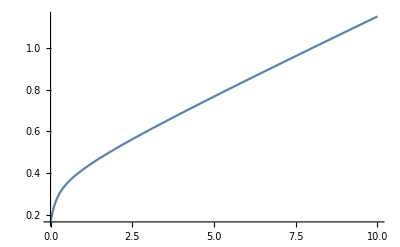

```mathematica
Plot[%336[x],{x,0.,10.}]
```

```mathematica
qr=Flatten[s]
```

{x_1[t]→InterpolatingFunction[…][t],y_1[t]→InterpolatingFunction[…][t],z_1[t]→InterpolatingFunction[…][t],x_2[t]→InterpolatingFunction[…][t],y_2[t]→InterpolatingFunction[…][t],z_2[t]→InterpolatingFunction[…][t],x_3[t]→InterpolatingFunction[…][t],y_3[t]→InterpolatingFunction[…][t],z_3[t]→InterpolatingFunction[…][t]}

```mathematica
ff=qr[[1]];First[ff]
```

x_1[t]

```mathematica
Plot[qr[[1]],{t,0,5},Epilog->Point[points]]
```

-Graphics-

{x_1[t]→InterpolatingFunction[…][t],y_1[t]→InterpolatingFunction[…][t],z_1[t]→InterpolatingFunction[…][t],x_2[t]→InterpolatingFunction[…][t],y_2[t]→InterpolatingFunction[…][t],z_2[t]→InterpolatingFunction[…][t],x_3[t]→InterpolatingFunction[…][t],y_3[t]→InterpolatingFunction[…][t],z_3[t]→InterpolatingFunction[…][t]}

```mathematica
Subscript[x, 1][t]
```

x_1[t]

```mathematica
NDSolve[{{Subscript[x, 1]''[t]==(Subscript[mas, 2] (Subscript[x, 1][t]-Subscript[x, 2][t]))/((Abs[Subscript[x, 1][t]-Subscript[x, 2][t]]^2+Abs[Subscript[y, 1][t]-Subscript[y, 2][t]]^2+Abs[Subscript[z, 1][t]-Subscript[z, 2][t]]^2)^(3/2))+(Subscript[mas, 3] (Subscript[x, 1][t]-Subscript[x, 3][t]))/((Abs[Subscript[x, 1][t]-Subscript[x, 3][t]]^2+Abs[Subscript[y, 1][t]-Subscript[y, 3][t]]^2+Abs[Subscript[z, 1][t]-Subscript[z, 3][t]]^2)^(3/2)),Subscript[y, 1]''[t]==(Subscript[mas, 2] (Subscript[y, 1][t]-Subscript[y, 2][t]))/((Abs[Subscript[x, 1][t]-Subscript[x, 2][t]]^2+Abs[Subscript[y, 1][t]-Subscript[y, 2][t]]^2+Abs[Subscript[z, 1][t]-Subscript[z, 2][t]]^2)^(3/2))+(Subscript[mas, 3] (Subscript[y, 1][t]-Subscript[y, 3][t]))/((Abs[Subscript[x, 1][t]-Subscript[x, 3][t]]^2+Abs[Subscript[y, 1][t]-Subscript[y, 3][t]]^2+Abs[Subscript[z, 1][t]-Subscript[z, 3][t]]^2)^(3/2)),Subscript[z, 1]''[t]==(Subscript[mas, 2] (Subscript[z, 1][t]-Subscript[z, 2][t]))/((Abs[Subscript[x, 1][t]-Subscript[x, 2][t]]^2+Abs[Subscript[y, 1][t]-Subscript[y, 2][t]]^2+Abs[Subscript[z, 1][t]-Subscript[z, 2][t]]^2)^(3/2))+(Subscript[mas, 3] (Subscript[z, 1][t]-Subscript[z, 3][t]))/((Abs[Subscript[x, 1][t]-Subscript[x, 3][t]]^2+Abs[Subscript[y, 1][t]-Subscript[y, 3][t]]^2+Abs[Subscript[z, 1][t]-Subscript[z, 3][t]]^2)^(3/2)),Subscript[x, 2]''[t]==(Subscript[mas, 1] (-Subscript[x, 1][t]+Subscript[x, 2][t]))/((Abs[-Subscript[x, 1][t]+Subscript[x, 2][t]]^2+Abs[-Subscript[y, 1][t]+Subscript[y, 2][t]]^2+Abs[-Subscript[z, 1][t]+Subscript[z, 2][t]]^2)^(3/2))+(Subscript[mas, 3] (Subscript[x, 2][t]-Subscript[x, 3][t]))/((Abs[Subscript[x, 2][t]-Subscript[x, 3][t]]^2+Abs[Subscript[y, 2][t]-Subscript[y, 3][t]]^2+Abs[Subscript[z, 2][t]-Subscript[z, 3][t]]^2)^(3/2)),Subscript[y, 2]''[t]==(Subscript[mas, 1] (-Subscript[y, 1][t]+Subscript[y, 2][t]))/((Abs[-Subscript[x, 1][t]+Subscript[x, 2][t]]^2+Abs[-Subscript[y, 1][t]+Subscript[y, 2][t]]^2+Abs[-Subscript[z, 1][t]+Subscript[z, 2][t]]^2)^(3/2))+(Subscript[mas, 3] (Subscript[y, 2][t]-Subscript[y, 3][t]))/((Abs[Subscript[x, 2][t]-Subscript[x, 3][t]]^2+Abs[Subscript[y, 2][t]-Subscript[y, 3][t]]^2+Abs[Subscript[z, 2][t]-Subscript[z, 3][t]]^2)^(3/2)),Subscript[z, 2]''[t]==(Subscript[mas, 1] (-Subscript[z, 1][t]+Subscript[z, 2][t]))/((Abs[-Subscript[x, 1][t]+Subscript[x, 2][t]]^2+Abs[-Subscript[y, 1][t]+Subscript[y, 2][t]]^2+Abs[-Subscript[z, 1][t]+Subscript[z, 2][t]]^2)^(3/2))+(Subscript[mas, 3] (Subscript[z, 2][t]-Subscript[z, 3][t]))/((Abs[Subscript[x, 2][t]-Subscript[x, 3][t]]^2+Abs[Subscript[y, 2][t]-Subscript[y, 3][t]]^2+Abs[Subscript[z, 2][t]-Subscript[z, 3][t]]^2)^(3/2)),Subscript[x, 3]''[t]==(Subscript[mas, 1] (-Subscript[x, 1][t]+Subscript[x, 3][t]))/((Abs[-Subscript[x, 1][t]+Subscript[x, 3][t]]^2+Abs[-Subscript[y, 1][t]+Subscript[y, 3][t]]^2+Abs[-Subscript[z, 1][t]+Subscript[z, 3][t]]^2)^(3/2))+(Subscript[mas, 2] (-Subscript[x, 2][t]+Subscript[x, 3][t]))/((Abs[-Subscript[x, 2][t]+Subscript[x, 3][t]]^2+Abs[-Subscript[y, 2][t]+Subscript[y, 3][t]]^2+Abs[-Subscript[z, 2][t]+Subscript[z, 3][t]]^2)^(3/2)),Subscript[y, 3]''[t]==(Subscript[mas, 1] (-Subscript[y, 1][t]+Subscript[y, 3][t]))/((Abs[-Subscript[x, 1][t]+Subscript[x, 3][t]]^2+Abs[-Subscript[y, 1][t]+Subscript[y, 3][t]]^2+Abs[-Subscript[z, 1][t]+Subscript[z, 3][t]]^2)^(3/2))+(Subscript[mas, 2] (-Subscript[y, 2][t]+Subscript[y, 3][t]))/((Abs[-Subscript[x, 2][t]+Subscript[x, 3][t]]^2+Abs[-Subscript[y, 2][t]+Subscript[y, 3][t]]^2+Abs[-Subscript[z, 2][t]+Subscript[z, 3][t]]^2)^(3/2)),Subscript[z, 3]''[t]==(Subscript[mas, 1] (-Subscript[z, 1][t]+Subscript[z, 3][t]))/((Abs[-Subscript[x, 1][t]+Subscript[x, 3][t]]^2+Abs[-Subscript[y, 1][t]+Subscript[y, 3][t]]^2+Abs[-Subscript[z, 1][t]+Subscript[z, 3][t]]^2)^(3/2))+(Subscript[mas, 2] (-Subscript[z, 2][t]+Subscript[z, 3][t]))/((Abs[-Subscript[x, 2][t]+Subscript[x, 3][t]]^2+Abs[-Subscript[y, 2][t]+Subscript[y, 3][t]]^2+Abs[-Subscript[z, 2][t]+Subscript[z, 3][t]]^2)^(3/2))},{Subscript[x, 1][0]==0.6224466321148838,Subscript[y, 1][0]==0.4877450347805474,Subscript[z, 1][0]==0.0226084761614469,Subscript[x, 2][0]==0.8320052719813535,Subscript[y, 2][0]==0.27922258827898827,Subscript[z, 2][0]==0.7650216980229831,Subscript[x, 3][0]==0.7204049326254853,Subscript[y, 3][0]==0.37990263160728777,Subscript[z, 3][0]==0.053052245166992584},{Subscript[x, 1]'[0]==0.4999389838956265,Subscript[y, 1]'[0]==0.6072891076313205,Subscript[z, 1]'[0]==0.5482498384110388,Subscript[x, 2]'[0]==0.21146012400162695,Subscript[y, 2]'[0]==0.953785635307101,Subscript[z, 2]'[0]==0.3993957749223931,Subscript[x, 3]'[0]==0.6217716035233403,Subscript[y, 3]'[0]==0.9041962193322581,Subscript[z, 3]'[0]==0.9170217524133133}},{Subscript[x, 1][t],Subscript[y, 1][t],Subscript[z, 1][t],Subscript[x, 2][t],Subscript[y, 2][t],Subscript[z, 2][t],Subscript[x, 3][t],Subscript[y, 3][t],Subscript[z, 3][t]},{t,0,10}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{{x_1''[t]==(mas_2 (x_1[t]-x_2[t]))/((Abs[x_1[t]-x_2[t]]^2+Abs[y_1[t]-y_2[t]]^2+Abs[z_1[t]-z_2[t]]^2)^(3/2))+(mas_3 (x_1[t]-x_3[t]))/((Abs[x_1[t]-x_3[t]]^2+Abs[y_1[t]-y_3[t]]^2+Abs[z_1[t]-z_3[t]]^2)^(3/2)),y_1''[t]==(mas_2 (y_1[t]-y_2[t]))/((Abs[x_1[t]-x_2[t]]^2+Abs[y_1[t]-y_2[t]]^2+Abs[z_1[t]-z_2[t]]^2)^(3/2))+(mas_3 (y_1[t]-y_3[t]))/((Abs[x_1[t]-x_3[t]]^2+Abs[y_1[t]-y_3[t]]^2+Abs[z_1[t]-z_3[t]]^2)^(3/2)),z_1''[t]==(mas_2 (z_1[t]-z_2[t]))/((Abs[x_1[t]-x_2[t]]^2+Abs[y_1[t]-y_2[t]]^2+Abs[z_1[t]-z_2[t]]^2)^(3/2))+(mas_3 (z_1[t]-z_3[t]))/((Abs[x_1[t]-x_3[t]]^2+Abs[y_1[t]-y_3[t]]^2+Abs[z_1[t]-z_3[t]]^2)^(3/2)),x_2''[t]==(mas_1 (-x_1[t]+x_2[t]))/((Abs[-x_1[t]+x_2[t]]^2+Abs[-y_1[t]+y_2[t]]^2+Abs[-z_1[t]+z_2[t]]^2)^(3/2))+(mas_3 (x_2[t]-x_3[t]))/((Abs[x_2[t]-x_3[t]]^2+Abs[y_2[t]-y_3[t]]^2+Abs[z_2[t]-z_3[t]]^2)^(3/2)),y_2''[t]==(mas_1 (-y_1[t]+y_2[t]))/((Abs[-x_1[t]+x_2[t]]^2+Abs[-y_1[t]+y_2[t]]^2+Abs[-z_1[t]+z_2[t]]^2)^(3/2))+(mas_3 (y_2[t]-y_3[t]))/((Abs[x_2[t]-x_3[t]]^2+Abs[y_2[t]-y_3[t]]^2+Abs[z_2[t]-z_3[t]]^2)^(3/2)),z_2''[t]==(mas_1 (-z_1[t]+z_2[t]))/((Abs[-x_1[t]+x_2[t]]^2+Abs[-y_1[t]+y_2[t]]^2+Abs[-z_1[t]+z_2[t]]^2)^(3/2))+(mas_3 (z_2[t]-z_3[t]))/((Abs[x_2[t]-x_3[t]]^2+Abs[y_2[t]-y_3[t]]^2+Abs[z_2[t]-z_3[t]]^2)^(3/2)),x_3''[t]==(mas_1 (-x_1[t]+x_3[t]))/((Abs[-x_1[t]+x_3[t]]^2+Abs[-y_1[t]+y_3[t]]^2+Abs[-z_1[t]+z_3[t]]^2)^(3/2))+(mas_2 (-x_2[t]+x_3[t]))/((Abs[-x_2[t]+x_3[t]]^2+Abs[-y_2[t]+y_3[t]]^2+Abs[-z_2[t]+z_3[t]]^2)^(3/2)),y_3''[t]==(mas_1 (-y_1[t]+y_3[t]))/((Abs[-x_1[t]+x_3[t]]^2+Abs[-y_1[t]+y_3[t]]^2+Abs[-z_1[t]+z_3[t]]^2)^(3/2))+(mas_2 (-y_2[t]+y_3[t]))/((Abs[-x_2[t]+x_3[t]]^2+Abs[-y_2[t]+y_3[t]]^2+Abs[-z_2[t]+z_3[t]]^2)^(3/2)),z_3''[t]==(mas_1 (-z_1[t]+z_3[t]))/((Abs[-x_1[t]+x_3[t]]^2+Abs[-y_1[t]+y_3[t]]^2+Abs[-z_1[t]+z_3[t]]^2)^(3/2))+(mas_2 (-z_2[t]+z_3[t]))/((Abs[-x_2[t]+x_3[t]]^2+Abs[-y_2[t]+y_3[t]]^2+Abs[-z_2[t]+z_3[t]]^2)^(3/2))},{x_1[0]==0.622447,y_1[0]==0.487745,z_1[0]==0.0226085,x_2[0]==0.832005,y_2[0]==0.279223,z_2[0]==0.765022,x_3[0]==0.720405,y_3[0]==0.379903,z_3[0]==0.0530522},{x_1'[0]==0.499939,y_1'[0]==0.607289,z_1'[0]==0.54825,x_2'[0]==0.21146,y_2'[0]==0.953786,z_2'[0]==0.399396,x_3'[0]==0.621772,y_3'[0]==0.904196,z_3'[0]==0.917022}},{x_1[t],y_1[t],z_1[t],x_2[t],y_2[t],z_2[t],x_3[t],y_3[t],z_3[t]},{t,0,10}]

```mathematica
Subscript[y, 1]'[0]==0.6072891076313205
```

y_1'[0]==0.607289

```mathematica
Thread[intpos=RandomReal[1,9]]
```

{0.559927,0.802649,0.501593,0.977308,0.922008,0.0612977,0.474085,0.769125,0.742716}

```mathematica
as:=k[r]
```

```mathematica
as[0]
```

k[r][0]

```mathematica
k[1]
```

k[t][t==1]

```mathematica
k[1][1]
```

```mathematica
ir[0]=RandomReal[1,9]
```

Set::write: Tag List in {0.0728992,0.850367,0.678864,0.746154,0.0681979,0.767069,0.0742811,0.0240607,0.311164}[0] is Protected.

{0.882618,0.0283679,0.881379,0.291158,0.984095,0.941659,0.270713,0.501792,0.792664}

```mathematica
RandomReal[1,9]
```

{0.697996,0.702678,0.215625,0.563627,0.358816,0.476095,0.101163,0.177931,0.454115}

OneIdentity[10]

x_1''[t]==(mass_2 (x_1[t]-x_2[t]))/((Abs[x_1[t]-x_2[t]]^2+Abs[y_1[t]-y_2[t]]^2+Abs[z_1[t]-z_2[t]]^2)^(3/2))+(mass_3 (x_1[t]-x_3[t]))/((Abs[x_1[t]-x_3[t]]^2+Abs[y_1[t]-y_3[t]]^2+Abs[z_1[t]-z_3[t]]^2)^(3/2))

{r_1''[t],r_2''[t],r_3''[t]}

If[1==n,(mass_m (po⟦n⟧-po⟦m⟧))/(po⟦n⟧-po⟦m⟧)^3,0]+If[2==n,(mass_m (po⟦n⟧-po⟦m⟧))/(po⟦n⟧-po⟦m⟧)^3,0]+If[3==n,(mass_m (po⟦n⟧-po⟦m⟧))/(po⟦n⟧-po⟦m⟧)^3,0]

{a==ol,ad==og,af==gd}

4

```mathematica
[Subscript[r, 1][t]-Subscript[r, 2][t]]
```

```mathematica
Information[eqs]
```

```mathematica
&&
```

```mathematica
Information[&&]
```

```mathematica
m≠1
```